Solution to VoronoiTessellation Practice

Here is a do loop that will print all 3 types of voronoi colouring patterns with variable stats option and for a list of datasets.

Data set #1

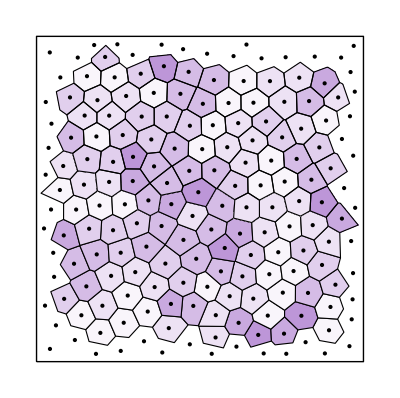
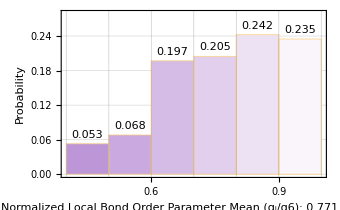

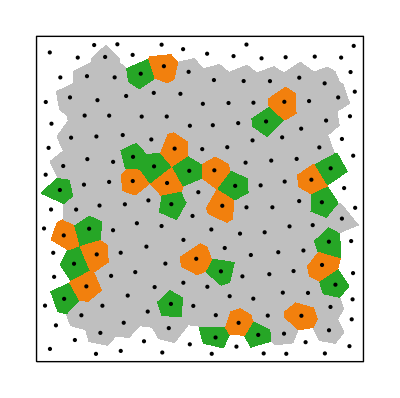
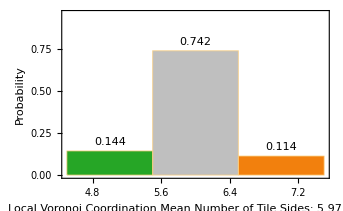

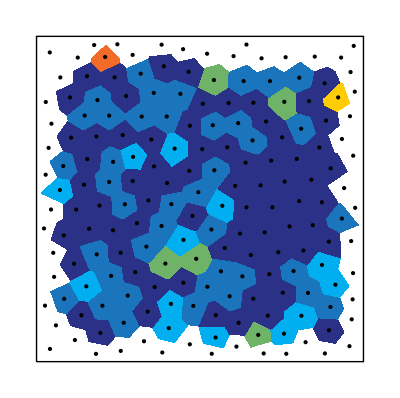
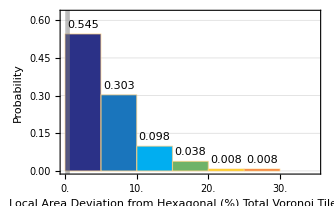

Data set #2

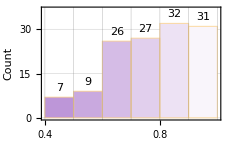
{-Graphics-,-Graphics-}

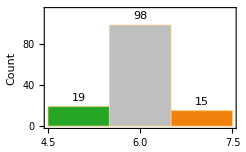
{-Graphics-,-Graphics-}

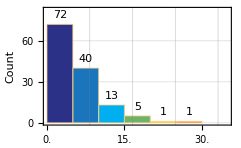
{-Graphics-,-Graphics-}

```mathematica
myData = Import["xyl200.csv"];
combinedData = {myData,myData};
statOptions = {"Probability", "Count"};


Do[ Print["Data set #"<>ToString@i];Print@  PlotVoronoiTessellations[combinedData[[i]], stats->statOptions[[i]] , type->#] &/@{"bop","coord", "vor"}, 

{i,Length@combinedData}]
```

| Related Guides
▪"disLocate"paclet:disLocate/guide/disLocate